```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/sarp/Desktop/Binary_NS_detection_Work

```mathematica
$MinPrecision=16
$WorkingPrecison=16
```

16

16

```mathematica
tmp=Import["H-H1_LOSC_4_V2-1126259446-32.hdf5"];
```

```mathematica
Length[tmp]
```

15

```mathematica
tmp[[15]]
```

/strain/Strain

```mathematica
strain=Import["H-H1_LOSC_4_V2-1126257414-4096.hdf5",{"Datasets","/strain/Strain"}];
```

```mathematica
Length[strain]
```

16777216

```mathematica
Precision[strain[[2]]]
```

MachinePrecision

```mathematica
H1data="H-H1_LOSC_4_V2-1126259446-32.hdf5";
```

```mathematica
L1data="L-L1_LOSC_4_V2-1126259446-32.hdf5";
```

```mathematica
H1strain=SetPrecision[Import[H1data,{"Datasets","/strain/Strain"}],16];
H1attributes=Import[H1data,{"Attributes","/strain/Strain"}]
```

{Npoints→131072,Xlabel→ .86.82.02.00.00.00.00,Xspacing→0.000244141,Xstart→1126259446,Xunits→@.86.82.02.00.00.00.00,Ylabel→`.86.82.02.00.00.00.00,Yunits→.80.86.82.02.00.00.00.00}

```mathematica
H1strain[[5]]
```

2.132240376792458×10^-19

```mathematica
L1strain=SetPrecision[Import[L1data,{"Datasets","/strain/Strain"}],16];
L1attributes=Import[L1data,{"Attributes","/strain/Strain"}]
```

{Npoints→131072,Xlabel→ .86.82.02.00.00.00.00,Xspacing→0.000244141,Xstart→1126259446,Xunits→.00Á?.02.00.00.00.00,Ylabel→°G.02.00.00.00.00,Yunits→ ìF.02.00.00.00.00}

```mathematica
{t0,dtfloat,n}={"Xstart","Xspacing","Npoints"}/.H1attributes
```

{1126259446,0.000244141,131072}

```mathematica
dt=1/4096;
dt-dtfloat
```

0.

```mathematica
time=t0+(Range[n]-1) dt;
```

```mathematica
N[time[[12]],16]
```

1.126259446002686×10^9

```mathematica
tEvent=1126259462.39;(*2015-09-14T09:50:45 GMT*)
tWindow=5;
tFilter=Flatten[Position[tWindow-Abs[time-tEvent],_Real?Positive]];
tCloseFilter=Flatten[Position[0.1-Abs[time-tEvent],_Real?Positive]];
```

## Plot the H1 and L1 strains in a 10 second interval centred on the event (note the very low frequency offset in L1)

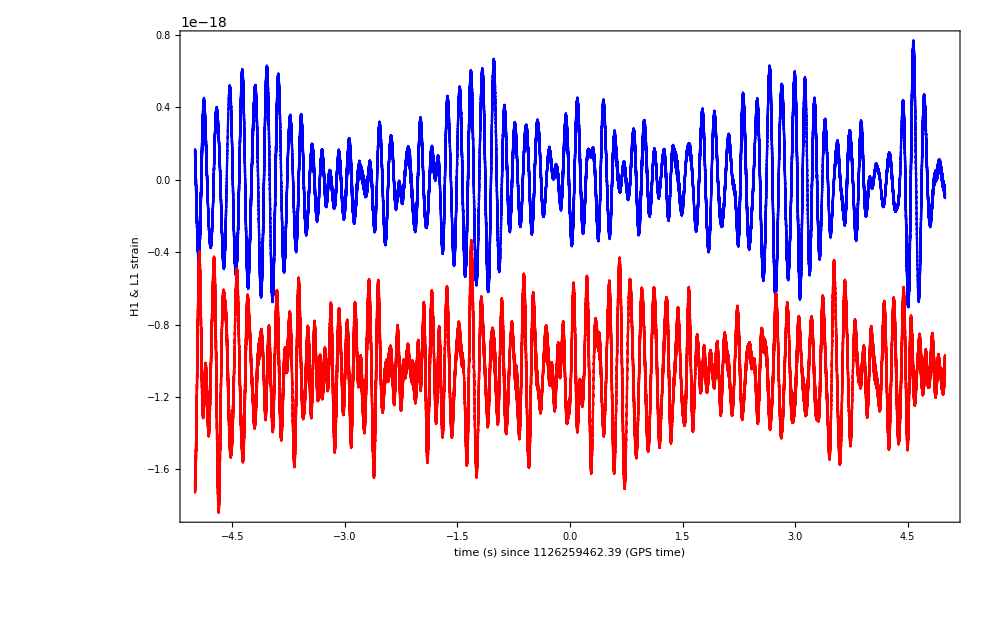

```mathematica
ListPlot[{Transpose[{time[[tFilter]]-tEvent,H1strain[[tFilter]]}],Transpose[{time[[tFilter]]-tEvent,L1strain[[tFilter]]}]},Joined->True,Frame->True,PlotStyle->{Directive[Blue],Directive[Red]},FrameLabel->{"time (s) since "<>ToString[AccountingForm[tEvent,12]]<>" (GPS time)","H1 & L1 strain"},ImageSize->1000]
```

## Estimate the Amplitude Spectral Density from the data (ignoring the fact that it contains a signal!)

```mathematica
H1strain[[1]]
```

2.177040281449375×10^-19

```mathematica
Precision[H1strain]
```

16.

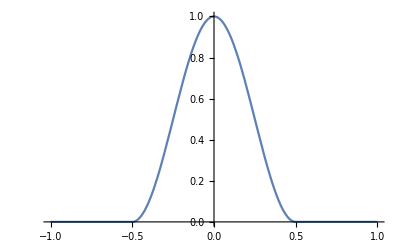

```mathematica
Plot[HannWindow[x],{x,-1,1}]
```

```mathematica
4097/2.
```

2048.5

```mathematica
HannWindowTable=Table[HannWindow[(i-2048.5`16)/4096],{i,1,4096}];
```

```mathematica
Table[i,{i,1,5}] Table[j^2,{j,1,5}]
```

{1,8,27,64,125}

```mathematica
Length[H1strain]/4096
```

32

```mathematica
MeanHann=Mean[Abs[Fourier[HannWindowTable]]^2]
```

0.375

```mathematica
AOH1specHann=Mean[Table[Abs[Fourier[H1strain[[1+4096n;;4096(n+1)]]HannWindowTable]]^2,{n,0,31}]]/MeanHann;
AOL1specHann=Mean[Table[Abs[Fourier[L1strain[[1+4096n;;4096(n+1)]]HannWindowTable]]^2,{n,0,31}]]/MeanHann;
```

```mathematica
Length[AOH1specHann]
```

4096

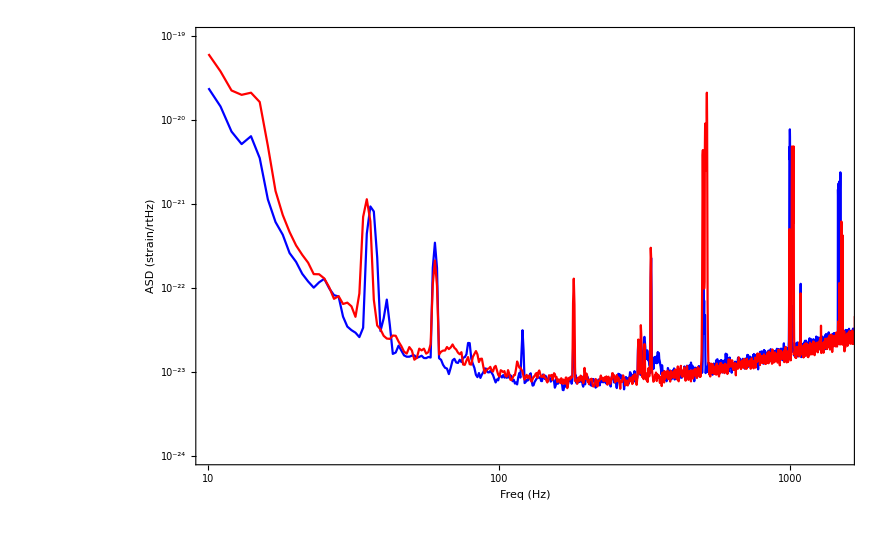

```mathematica
ListLogLogPlot[{Table[{i,Sqrt[2 dt AOH1specHann[[i+1]]]},{i,10,2000}],Table[{i,Sqrt[2 dt AOL1specHann[[i+1]]]},{i,10,2000}]},Joined->True,GridLines->Automatic,Frame->True,PlotStyle->{Directive[Blue],Directive[Red]},FrameLabel->{"Freq (Hz)","ASD (strain/rtHz)"},PlotRange->{{10,1500},{10^-24,10^-19}}]
```

```mathematica
H1specHann=PeriodogramArray[H1strain,1/dt,1/dt,HannWindow];
L1specHann=PeriodogramArray[L1strain,1/dt,1/dt,HannWindow];
```

```mathematica
{H1specHann[[101]],AOH1specHann[[101]]}2 dt (* This is identical to H1_Pxx *)
```

{8.47915×10^-47,8.480443510976717×10^-47}

```mathematica
H1specHann[[11]]
```

1.17046×10^-36

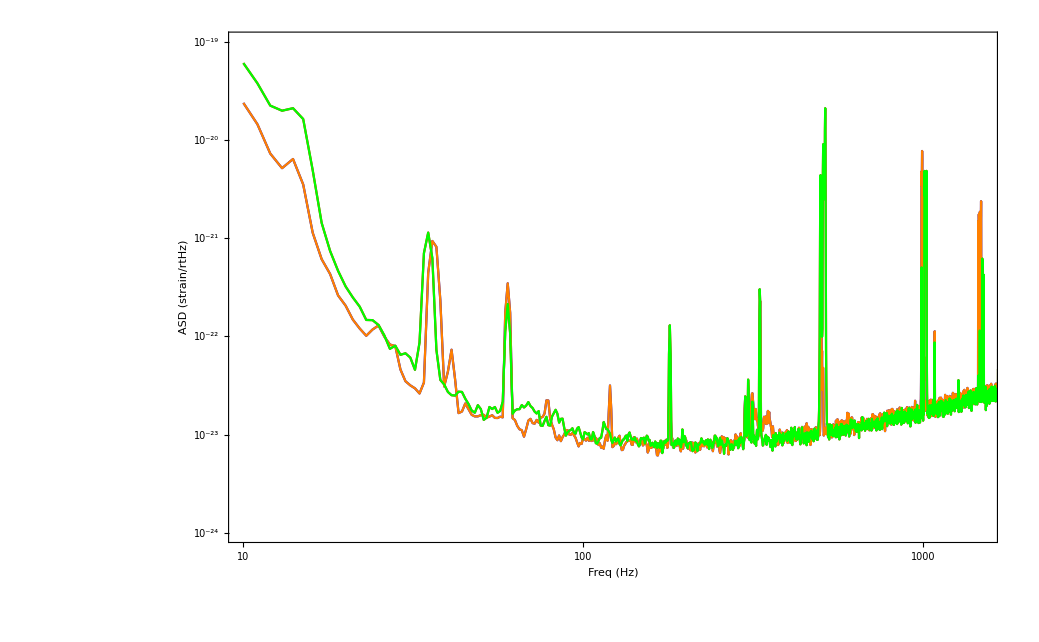

```mathematica
pList=ListLogLogPlot[{Table[{i,Sqrt[2 dt H1specHann[[i+1]]]},{i,10,2000}],Table[{i,Sqrt[2 dt L1specHann[[i+1]]]},{i,10,2000}],Table[{i,Sqrt[2 dt AOH1specHann[[i+1]]]},{i,10,2000}],Table[{i,Sqrt[2 dt AOL1specHann[[i+1]]]},{i,10,2000}]},Joined->True,GridLines->Automatic,Frame->True,PlotStyle->{Directive[Blue],Directive[Red],Directive[Orange],Directive[Green]},FrameLabel->{"Freq (Hz)","ASD (strain/rtHz)"},PlotRange->{{10,1500},{10^-24,10^-19}}]
```

## Construct a whitening filter

```mathematica
H1PSDHannInterShifted=Interpolation[2 dt H1specHann, InterpolationOrder->1];
L1PSDHannInterShifted=Interpolation[2 dt L1specHann, InterpolationOrder->1];
H1PSDHannInter[f_]:=H1PSDHannInterShifted[f+1]
L1PSDHannInter[f_]:=L1PSDHannInterShifted[f+1]

H1ASDHannInterShifted=Interpolation[Sqrt[2 dt H1specHann], InterpolationOrder->1];
L1ASDHannInterShifted=Interpolation[Sqrt[2 dt L1specHann], InterpolationOrder->1];
H1ASDHannInter[f_]:=H1ASDHannInterShifted[f+1]
L1ASDHannInter[f_]:=L1ASDHannInterShifted[f+1]

AOH1PSDHannInterShifted=Interpolation[2 dt AOH1specHann, InterpolationOrder->1];
AOL1PSDHannInterShifted=Interpolation[2 dt AOL1specHann, InterpolationOrder->1];
AOH1PSDHannInter[f_]:=AOH1PSDHannInterShifted[f+1]
AOL1PSDHannInter[f_]:=AOL1PSDHannInterShifted[f+1]

AOH1ASDHannInterShifted=Interpolation[Sqrt[2 dt AOH1specHann], InterpolationOrder->1];
AOL1ASDHannInterShifted=Interpolation[Sqrt[2 dt AOL1specHann], InterpolationOrder->1];
AOH1ASDHannInter[f_]:=AOH1ASDHannInterShifted[f+1]
AOL1ASDHannInter[f_]:=AOL1ASDHannInterShifted[f+1]
```

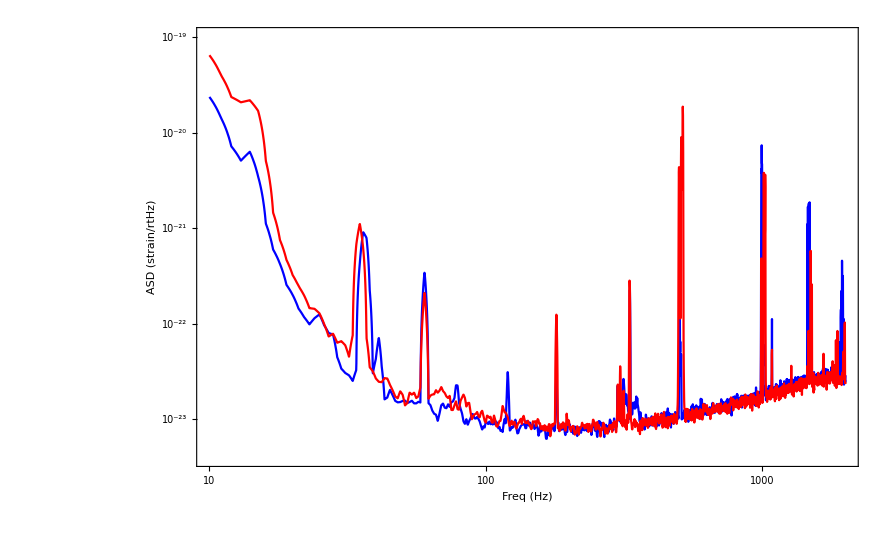

```mathematica
pInter=LogLogPlot[{H1ASDHannInter[f],L1ASDHannInter[f]},{f,10,2000},GridLines->Automatic,Frame->True,PlotStyle->{Directive[Blue],Directive[Red]},FrameLabel->{"Freq (Hz)","ASD (strain/rtHz)"},PlotRange->{{10,2000},All}]
```

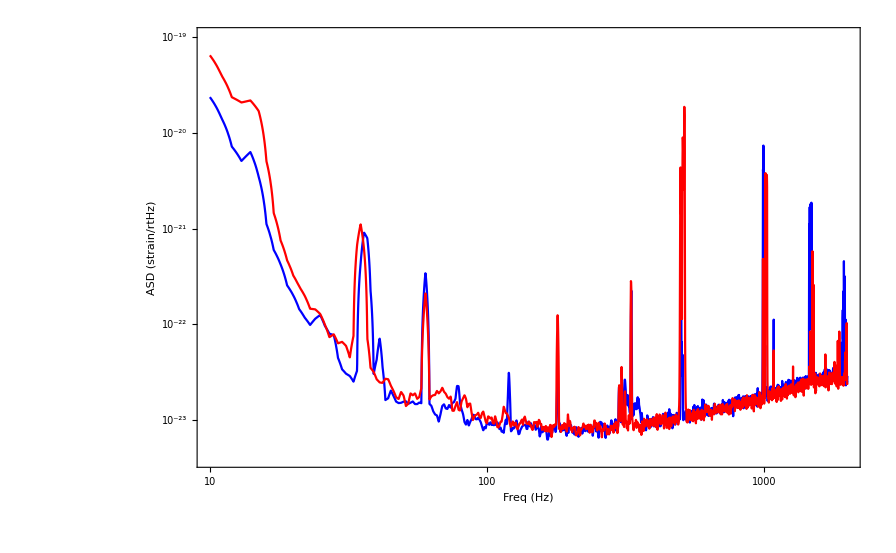

```mathematica
pInter=LogLogPlot[{AOH1ASDHannInter[f],AOL1ASDHannInter[f]},{f,10,2000},GridLines->Automatic,Frame->True,PlotStyle->{Directive[Blue],Directive[Red]},FrameLabel->{"Freq (Hz)","ASD (strain/rtHz)"},PlotRange->{{10,2000},All}]
```

```mathematica
(* Show[{pList,pInter}] *)
```

```mathematica
√(H1specHann[[11]]2 dt)
```

2.36508×10^-20

```mathematica
H1specHann[[11]]2 dt
```

5.59361×10^-40

```mathematica
AOH1ASDHannInter[10]
```

2.365076643477296×10^-20

```mathematica
nFFT=Length[Fourier[H1strain]]
```

131072

```mathematica
With[{i=1000},Fourier[H1strain][[i]]/AOH1ASDHannInter[i/Length[Fourier[H1strain]]]]
```

0.06633828702307898+0.5768648586085901 ⅈ

```mathematica
dtPy=1/4096;
nPy=nFFT;
```

```mathematica
Freqs=Table[i-1,{i,1,nPy/2+1}]/(dtPy*nPy)
```

{0,1/32,1/16,3/32,1/8,5/32,3/16,7/32,1/4,9/32,5/16,11/32,3/8,13/32,7/16,15/32,1/2,17/32,9/16,19/32,5/8,21/32,11/16,23/32,3/4,25/32,13/16,27/32,7/8,29/32,15/16,31/32,1,33/32,17/16,35/32,9/8,37/32,19/16,39/32,5/4,41/32,21/16,43/32,11/8,45/32,23/16,47/32,3/2,49/32,25/16,51/32,13/8,53/32,27/16,55/32,7/4,57/32,29/16,59/32,15/8,61/32,31/16,63/32,2,65/32,33/16,67/32,17/8,65399,16367/8,65469/32,32735/16,65471/32,2046,65473/32,32737/16,65475/32,16369/8,65477/32,32739/16,65479/32,8185/4,65481/32,32741/16,65483/32,16371/8,65485/32,32743/16,65487/32,4093/2,65489/32,32745/16,65491/32,16373/8,65493/32,32747/16,65495/32,8187/4,65497/32,32749/16,65499/32,16375/8,65501/32,32751/16,65503/32,2047,65505/32,32753/16,65507/32,16377/8,65509/32,32755/16,65511/32,8189/4,65513/32,32757/16,65515/32,16379/8,65517/32,32759/16,65519/32,4095/2,65521/32,32761/16,65523/32,16381/8,65525/32,32763/16,65527/32,8191/4,65529/32,32765/16,65531/32,16383/8,65533/32,32767/16,65535/32,2048}
 |  |  |  |

```mathematica
N[1/32]
```

0.03125

```mathematica
FTtest=RandomReal[{0,1},10]
FTtest-InverseFourier[Fourier[FTtest]]
```

{0.210319,0.237228,0.147604,0.544946,0.940096,0.507582,0.0399906,0.502459,0.0281027,0.296899}

{-8.32667×10^-17,5.55112×10^-17,5.55112×10^-17,0.,0.,0.,1.17961×10^-16,0.,-8.32667×10^-17,0.}

10

```mathematica
RFFT=Fourier[FTtest][[1;;1+Length[FTtest]/2]]
FTtest-InverseFourier[Join[RFFT,Conjugate[Reverse[Take[RFFT,{2,Length[FTtest]/2}]]]]]
```

{1.09264+0. ⅈ,-0.293277+0.204933 ⅈ,0.0620759-0.274338 ⅈ,0.172586+0.222652 ⅈ,-0.0408445-0.20156 ⅈ,-0.228634+0. ⅈ}

{-8.32667×10^-17,5.55112×10^-17,5.55112×10^-17,0.,0.,0.,1.17961×10^-16,0.,-8.32667×10^-17,0.}

{1.06066+0. ⅈ,0.-0.353553 ⅈ,-0.353553+0.707107 ⅈ,0.+0.353553 ⅈ,-0.353553+0. ⅈ,0.-0.353553 ⅈ,-0.353553-0.707107 ⅈ,0.+0.353553 ⅈ}

```mathematica
Precision[N[H1strain[[11]],16]]
```

16.

```mathematica
H1strainFFT=Fourier[SetPrecision[H1strain,16],FourierParameters->{1,-1}];
```

```mathematica
H1strainFFT[[13]]
```

2.965677125737689×10^-17-9.582884360104575×10^-18 ⅈ

```mathematica
(5.760829047396718*^-17+5.81643816905496*^-17 ⅈ)/(-2.19510583×10^-17+9.96326741×10^-17 ⅈ)
```

0.435269-0.674105 ⅈ

```mathematica
Freqs[[321;;329]]
```

{10,321/32,161/16,323/32,81/8,325/32,163/16,327/32,41/4}

```mathematica
H1ASDHannInter[Freqs[[321;;329]]] /√(2 dt)
```

{1.07031×10^-18,1.05719×10^-18,1.04406×10^-18,1.03093×10^-18,1.01781×10^-18,1.00468×10^-18,9.91552×10^-19,9.78425×10^-19,9.65298×10^-19}

```mathematica
AOH1ASDHannInter[Freqs[[321;;329]]] /√(2 dt)
```

{1.070311508882377×10^-18,1.057182971362308×10^-18,1.044054433842238×10^-18,1.030925896322168×10^-18,1.017797358802098×10^-18,1.004668821282028×10^-18,9.915402837619582×10^-19,9.784117462418883×10^-19,9.652832087218184×10^-19}

```mathematica
H1strainFFT[[321;;329]]
```

{4.523561808095946×10^-16+1.839037104500205×10^-17 ⅈ,3.336460749049189×10^-16+2.628845204336669×10^-16 ⅈ,6.02584372662075×10^-17+1.590905798810972×10^-16 ⅈ,2.816828973205024×10^-17-5.945326604783875×10^-17 ⅈ,1.495560123794089×10^-16-5.368659285415702×10^-16 ⅈ,4.303260709186434×10^-16-7.043711839036885×10^-17 ⅈ,1.559797709813124×10^-16+6.708468088263142×10^-17 ⅈ,1.586220971861763×10^-17-2.451566474432508×10^-16 ⅈ,-2.751769121859924×10^-16-1.407193068366351×10^-16 ⅈ}

```mathematica
dt
```

1/4096

```mathematica
H1WhitenedRFFT=Quiet[Table[H1strainFFT[[i]]/(H1ASDHannInter[Freqs[[i]]] /√(2 dt)),{i,nFFT/2+1}],{InterpolatingFunction::dmval}];
```

```mathematica
NewH1WhitenedRFFT=Quiet[Table[H1strainFFT[[i]]/√(H1PSDHannInter[Freqs[[i]]] /(2 dt)),{i,nFFT/2+1}],{InterpolatingFunction::dmval}];
```

```mathematica
AOH1WhitenedRFFT=Quiet[Table[H1strainFFT[[i]]/(AOH1ASDHannInter[Freqs[[i]]] /√(2 dt)),{i,nFFT/2+1}],{InterpolatingFunction::dmval}];
```

```mathematica
AONewH1WhitenedRFFT=Quiet[Table[H1strainFFT[[i]]/√(AOH1PSDHannInter[Freqs[[i]]] /(2 dt)),{i,nFFT/2+1}],{InterpolatingFunction::dmval}];
```

```mathematica
H1strainFFT[[32]]
```

1.327811367586784×10^-17-4.349656326080285×10^-18 ⅈ

```mathematica
√(H1PSDHannInter[Freqs[[32]]] /(2 dt))
```

5.44203×10^-19

```mathematica
H1WhitenedRFFT[[321;;329]]
```

{422.639+17.1822 ⅈ,315.598+248.664 ⅈ,57.7155+152.377 ⅈ,27.3231-57.6694 ⅈ,146.94-527.474 ⅈ,428.322-70.1091 ⅈ,157.309+67.6562 ⅈ,16.212-250.563 ⅈ,-285.069-145.778 ⅈ}

```mathematica
NewH1WhitenedRFFT[[321;;329]]
```

{422.639+17.1822 ⅈ,314.847+248.072 ⅈ,57.4437+151.659 ⅈ,27.1324-57.2669 ⅈ,145.59-522.628 ⅈ,423.47-69.3149 ⅈ,155.201+66.7499 ⅈ,15.9625-246.707 ⅈ,-280.139-143.257 ⅈ}

```mathematica
AOH1WhitenedRFFT[[321;;329]]
```

{422.6397427810025+17.18226039090744 ⅈ,315.5991762475854+248.665110538915 ⅈ,57.71580035769751+152.3776679876987 ⅈ,27.32329242338439-57.66977651831089 ⅈ,146.9408532907077-527.4782095852925 ⅈ,428.326292010851-70.10978831858854 ⅈ,157.3105737968775+67.65704024460657 ⅈ,16.21220286811243-250.5659282862308 ⅈ,-285.0737583536426-145.7803322021615 ⅈ}

```mathematica
AONewH1WhitenedRFFT[[321;;329]]
```

{422.6397427810025+17.18226039090744 ⅈ,314.8474734630114+248.0728331501051 ⅈ,57.44395271419154+151.6599527397308 ⅈ,27.13255586674295-57.26719931696418 ⅈ,145.5905787147861-522.6310864074616 ⅈ,423.4730178805758-69.31538921614666 ⅈ,155.2025951548438+66.7504286140178 ⅈ,15.96267342147061-246.7093532148976 ⅈ,-280.1423891298627-143.2585404812892 ⅈ}

```mathematica
H1WhitenedFFT=Join[H1WhitenedRFFT,Conjugate[Reverse[Take[H1WhitenedRFFT,{2,nFFT/2}]]]];
```

```mathematica
NewH1WhitenedFFT=Join[NewH1WhitenedRFFT,Conjugate[Reverse[Take[NewH1WhitenedRFFT,{2,nFFT/2}]]]];
```

```mathematica
AOH1WhitenedFFT=Join[AOH1WhitenedRFFT,Conjugate[Reverse[Take[AOH1WhitenedRFFT,{2,nFFT/2}]]]];
```

```mathematica
AONewH1WhitenedFFT=Join[AONewH1WhitenedRFFT,Conjugate[Reverse[Take[AONewH1WhitenedRFFT,{2,nFFT/2}]]]];
```

```mathematica
H1strainWhitened=InverseFourier[H1WhitenedFFT,FourierParameters->{1,-1}]
```

{138.504-1.07553×10^-16 ⅈ,219.714-1.66187×10^-14 ⅈ,220.374-2.01228×10^-15 ⅈ,195.046-1.72952×10^-14 ⅈ,200.791-4.41919×10^-15 ⅈ,192.022+6.89553×10^-15 ⅈ,172.951-5.44012×10^-15 ⅈ,156.951-2.92239×10^-15 ⅈ,131056,-152.406+1.35626×10^-14 ⅈ,-175.312+2.66168×10^-14 ⅈ,-165.951+1.35687×10^-14 ⅈ,-180.396+1.25944×10^-14 ⅈ,-196.615+2.37587×10^-14 ⅈ,-198.239+5.31767×10^-15 ⅈ,-189.984+1.88921×10^-14 ⅈ,-112.478-7.00012×10^-15 ⅈ}
 |  |  |  |

```mathematica
NewH1strainWhitened=Chop[InverseFourier[NewH1WhitenedFFT,FourierParameters->{1,-1}]]
```

{138.274,219.184,219.709,194.501,200.225,191.403,172.302,156.426,137.872,134.372,122.548,84.3048,79.7261,73.5655,55.8696,42.3802,33.1175,32.0945,42.1959,26.4023,27.2214,131030,-38.6762,-33.9328,-35.9391,-26.801,-28.797,-50.7297,-59.5754,-56.3177,-81.2566,-98.5849,-112.427,-125.698,-129.599,-151.95,-174.93,-165.575,-179.844,-196.1,-197.866,-189.783,-112.293}
 |  |  |  |

```mathematica
AOH1strainWhitened=InverseFourier[AOH1WhitenedFFT,FourierParameters->{1,-1}]
```

{138.505684829841,219.7162022313703,220.3743060966928,195.0469386606597,200.793818607764,192.023956080494,172.9511656994734,156.9516898188405,138.3430317902494,131055,-152.4063004716532,-175.312587949668,-165.9544143217281,-180.3984520111862,-196.6149400148644,-198.2404036133964,-189.9861097519988,-112.4787508428163}
 |  |  |  |

```mathematica
AONewH1strainWhitened=Chop[InverseFourier[AONewH1WhitenedFFT,FourierParameters->{1,-1}]]
```

{138.2753996769468,219.1863932657848,219.7099501742381,194.5016556177539,200.2276204131008,191.4055562595965,172.3019949206072,156.4263469346997,137.8740062365416,131055,-151.9497209443222,-174.9303698298831,-165.5780639555413,-179.8461234332493,-196.1001100369295,-197.8667995066539,-189.784967198108,-112.2934858161196}
 |  |  |  |

```mathematica
NewH1strainWhitened[[46655;;46661]]
```

{0.504528,-1.08236,0.321088,0.793112,0.214645,-0.848405,-0.678477}

```mathematica
AONewH1strainWhitened[[46655;;46661]]
```

{0.5045829004231187,-1.082249274830788,0.3210569031910233,0.7932196939039438,0.2148908214401616,-0.8482921129788111,-0.6784340779024236}

```mathematica
WhitenedH1specHann=PeriodogramArray[NewH1strainWhitened,1/dt,1/dt,HannWindow];
(* L1specHann=PeriodogramArray[L1strain,1/dt,1/dt,HannWindow]; *)
```

```mathematica
AOWhitenedH1specHann=PeriodogramArray[AONewH1strainWhitened,1/dt,1/dt,HannWindow];
(* Just to plot so don't care about accuracy *)
```

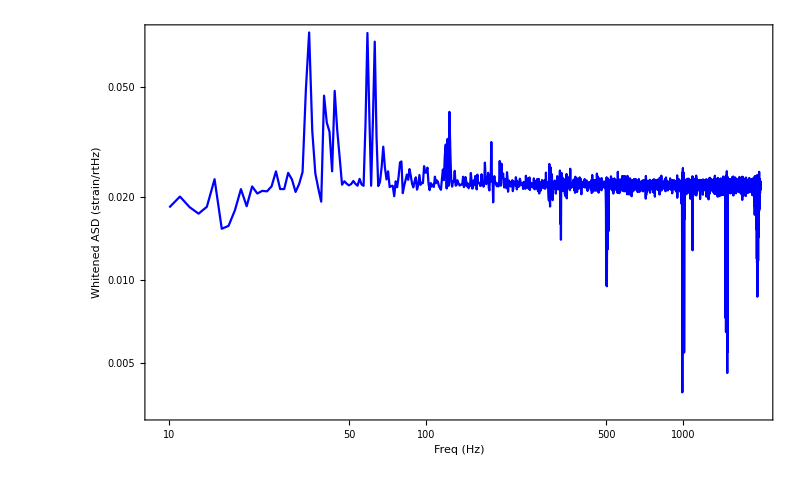

```mathematica
ListLogLogPlot[{Table[{i,Sqrt[2 dt AOWhitenedH1specHann[[i]]]},{i,10,2000}](*,Table[{i,Sqrt[2 dt L1specHann[[i]]]},{i,10,2000}]*)},Joined->True,GridLines->Automatic,Frame->True,PlotStyle->{Directive[Blue],Directive[Red]},FrameLabel->{"Freq (Hz)","Whitened ASD (strain/rtHz)"}]
```

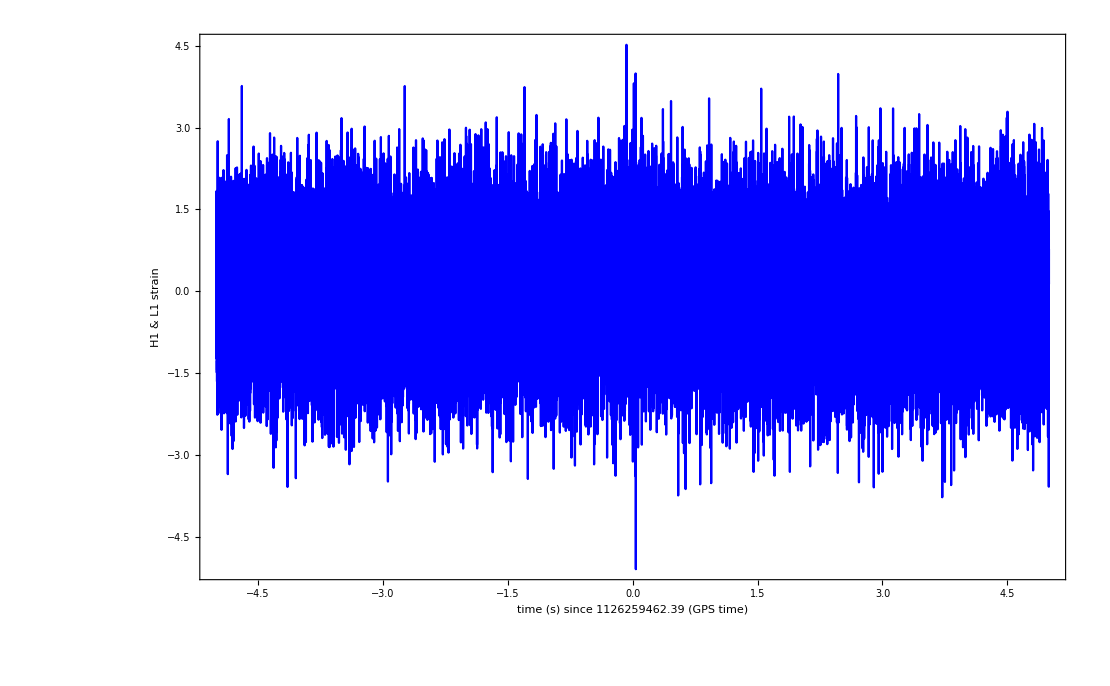

```mathematica
ListPlot[{Transpose[{time[[tFilter]]-tEvent,AONewH1strainWhitened[[tFilter]]}]},Joined->True,Frame->True,PlotStyle->{Directive[Blue],Directive[Red]},FrameLabel->{"time (s) since "<>ToString[AccountingForm[tEvent,12]]<>" (GPS time)","H1 & L1 strain"}]
```

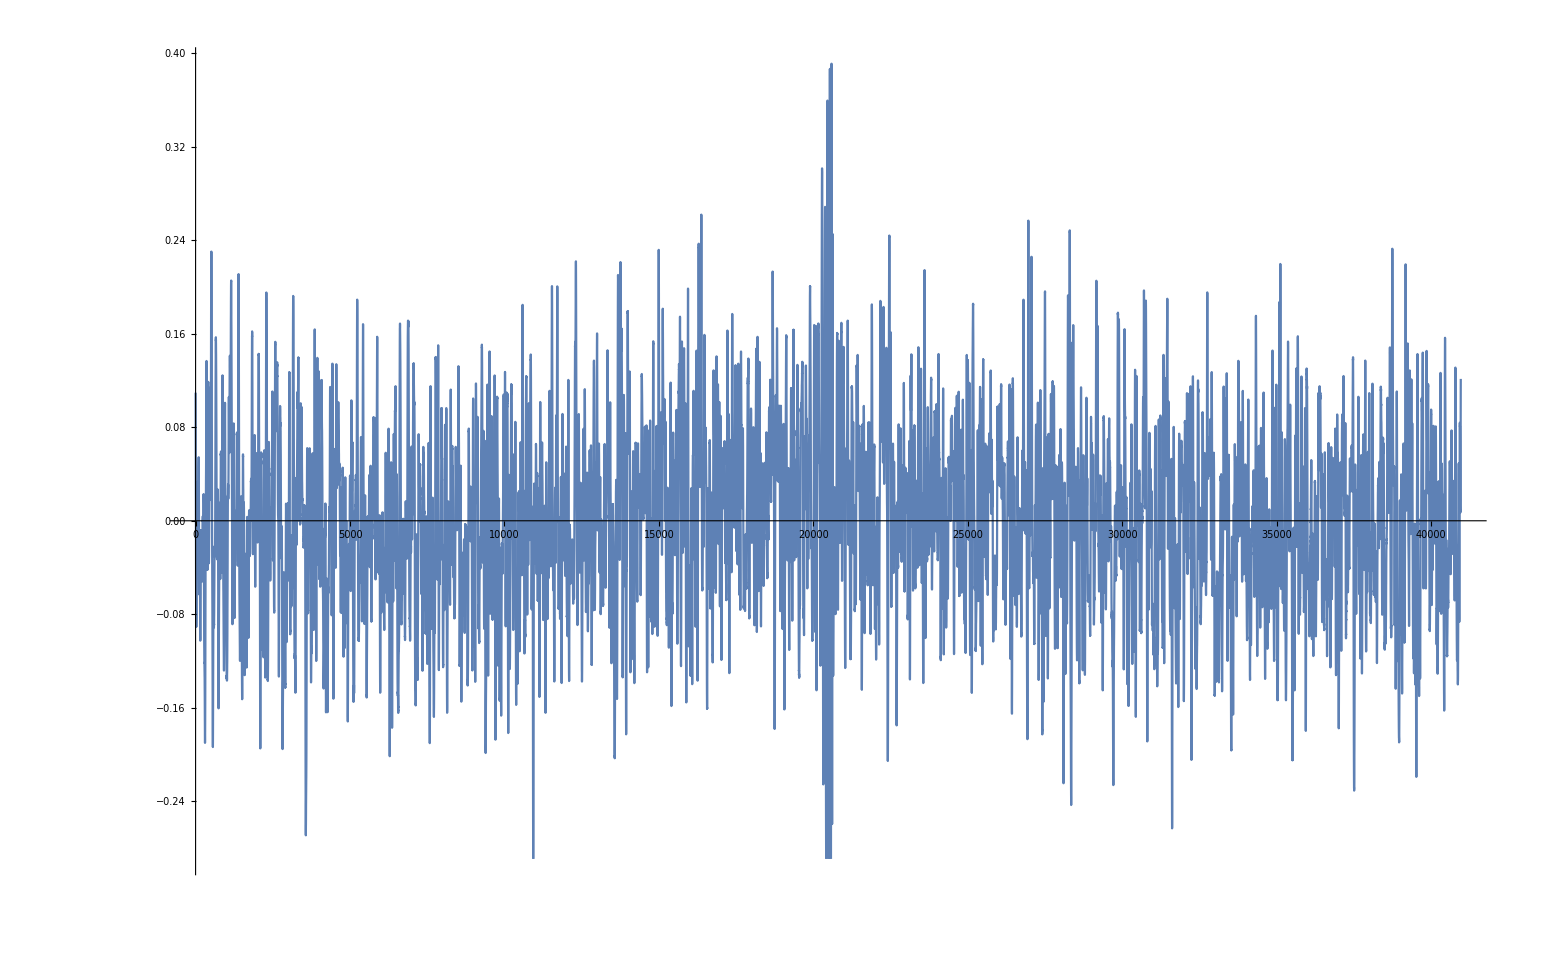

```mathematica
ListPlot[BandpassFilter[AONewH1strainWhitened,{20/4096,300/4096}][[tFilter]],Joined->True]
```

```mathematica
filteredstrain=BandpassFilter[AONewH1strainWhitened,{10/4096,200/4096}];
```

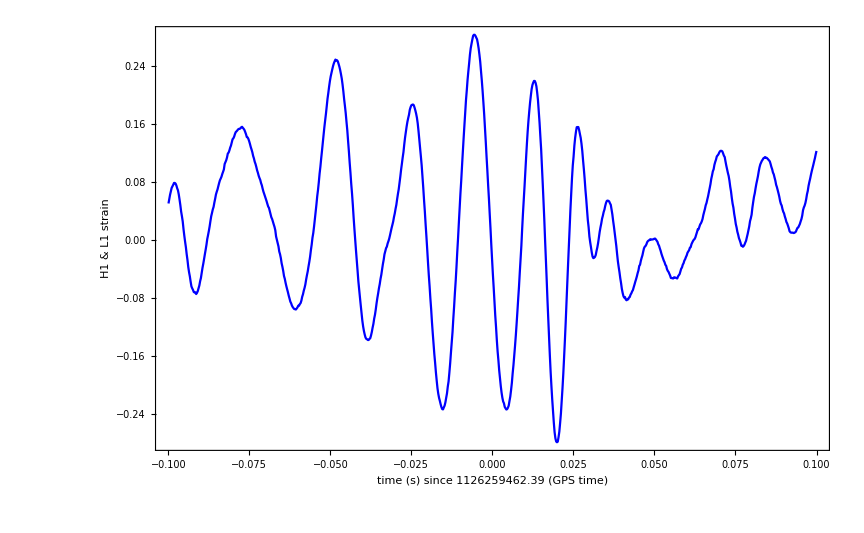

```mathematica
ListPlot[{Transpose[{time[[tCloseFilter]]-tEvent,filteredstrain[[tCloseFilter]]}]},Joined->True,Frame->True,PlotStyle->{Directive[Blue],Directive[Red]},FrameLabel->{"time (s) since "<>ToString[AccountingForm[tEvent,12]]<>" (GPS time)","H1 & L1 strain"}]
```

```mathematica
butter=ButterworthFilterModel[{"Bandpass",4,{10,200}}]
```

(1303210000 s^4)/((2000+s^2+190 s Cos[π/8]-190 ⅈ s Sin[π/8]) (2000+s^2+190 s Cos[π/8]+190 ⅈ s Sin[π/8]) (2000+s^2-190 ⅈ s Cos[π/8]+190 s Sin[π/8]) (2000+s^2+190 ⅈ s Cos[π/8]+190 s Sin[π/8]))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#s11130321000020001FalseFalseFalseAutomaticNoneAutomatic

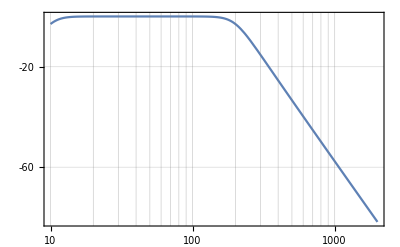

```mathematica
BodePlot[butter,{ω,10,2000},GridLines->Automatic,PlotLayout->"Magnitude"]
```

```mathematica
Length[RecurrenceFilter[ToDiscreteTimeModel[ButterworthFilterModel[{"Bandpass",4,{10,200}}],1],AONewH1strainWhitened]]
```

Precision::mnprec: Value 15.9607 would be inconsistent with $MinPrecision; bounding by $MinPrecision instead.

131072

Precision::mnprec: Value 15.9182 would be inconsistent with $MinPrecision; bounding by $MinPrecision instead.

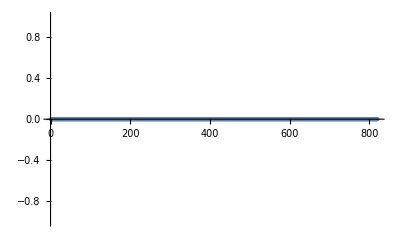

```mathematica
ListPlot[RecurrenceFilter[ToDiscreteTimeModel[ButterworthFilterModel[{"Bandpass",4,{10/4096,200/4096}}],1],AONewH1strainWhitened][[tCloseFilter]]]
```

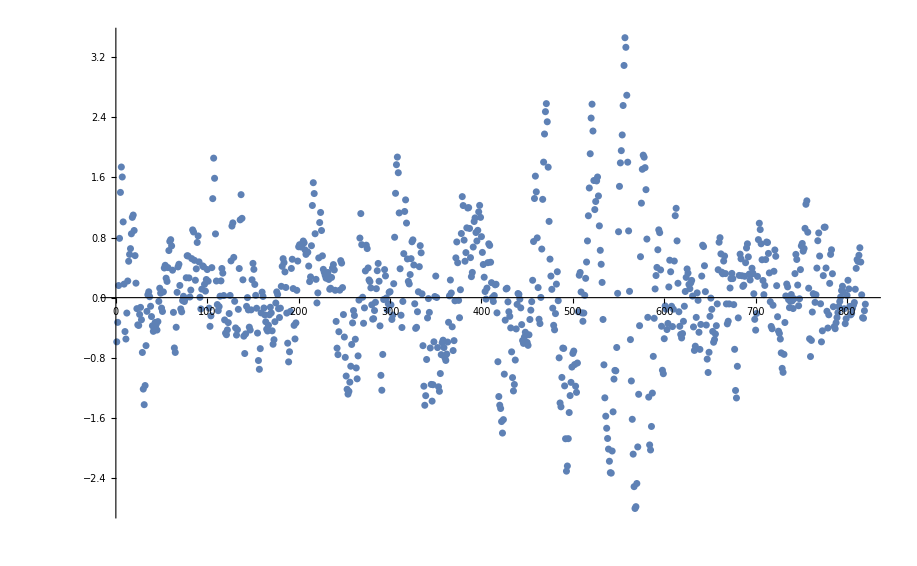

```mathematica
ListPlot[RecurrenceFilter[ToDiscreteTimeModel[ButterworthFilterModel[4],1],AONewH1strainWhitened][[tCloseFilter]]]
```

```mathematica
ButterworthFilterModel[{"Bandpass",4,{43,260}},s]
```

(2217373921 s^4)/((11180+s^2+217 s Cos[π/8]-217 ⅈ s Sin[π/8]) (11180+s^2+217 s Cos[π/8]+217 ⅈ s Sin[π/8]) (11180+s^2-217 ⅈ s Cos[π/8]+217 s Sin[π/8]) (11180+s^2+217 ⅈ s Cos[π/8]+217 s Sin[π/8]))TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s112217373921111801FalseFalseFalseAutomaticNoneAutomatic

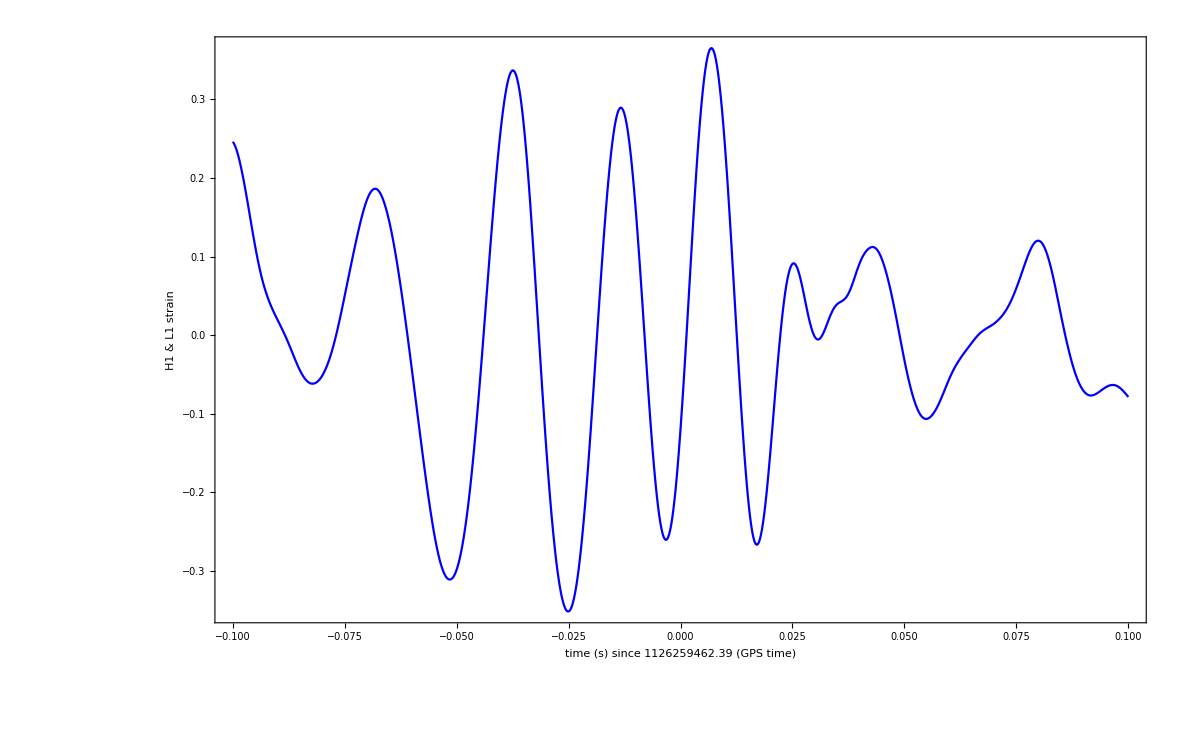

```mathematica
ListPlot[{Transpose[{time[[tCloseFilter]]-tEvent,RecurrenceFilter[ToDiscreteTimeModel[ButterworthFilterModel[{"Bandpass",4,{43.,260}},s],1/4096],AONewH1strainWhitened][[tCloseFilter]]}]},Joined->True,Frame->True,PlotStyle->{Directive[Blue],Directive[Red]},FrameLabel->{"time (s) since "<>ToString[AccountingForm[tEvent,12]]<>" (GPS time)","H1 & L1 strain"}]
```

```mathematica
RecurrenceFilter[ToDiscreteTimeModel[ButterworthFilterModel[{"Bandpass",4,{10.16,200.`16}},s],1],AONewH1strainWhitened[[45000;;45100]]]
```

{-0.0010767,0.00767041,-0.0269944,0.063539,-0.112123,0.155638,-0.174479,0.160706,-0.119385,0.0594987,0.0106516,-0.0828057,0.148415,-0.200022,0.232901,-0.244313,0.23357,-0.205054,0.166927,-0.124349,0.0754822,-0.0170605,-0.0453475,0.0984238,-0.132733,0.146999,-0.143002,0.121126,-0.0798024,0.0197169,0.0497776,-0.110965,0.146547,-0.149801,0.12673,-0.0873231,0.0393688,0.00696867,-0.0351856,0.028526,0.0175823,-0.0878803,0.153799,-0.191139,0.1932,-0.167521,0.123986,-0.0713974,0.0212663,0.0158301,-0.0364671,0.0407386,-0.0282327,0.00286271,0.0259917,-0.0501544,0.0648423,-0.0697852,0.0718125,-0.0755301,0.0718607,-0.0462175,-0.00574973,0.0763619,-0.151911,0.215771,-0.253629,0.262571,-0.253086,0.240114,-0.233644,0.235124,-0.238169,0.23456,-0.224279,0.219213,-0.233975,0.274569,-0.337263,0.412563,-0.485115,0.534387,-0.541179,0.494348,-0.395706,0.260204,-0.105798,-0.0543192,0.205006,-0.324169,0.393026,-0.408656,0.38671,-0.353661,0.332026,-0.330721,0.348755,-0.383395,0.432831,-0.492446,0.550597}

```mathematica
time[[45000;;45100]]-tEvent
```

{-5.40392,-5.40367,-5.40343,-5.40318,-5.40294,-5.4027,-5.40245,-5.40221,-5.40196,-5.40172,-5.40147,-5.40123,-5.40099,-5.40074,-5.4005,-5.40025,-5.40001,-5.39977,-5.39952,-5.39928,-5.39903,-5.39879,-5.39855,-5.3983,-5.39806,-5.39781,-5.39757,-5.39732,-5.39708,-5.39684,-5.39659,-5.39635,-5.3961,-5.39586,-5.39562,-5.39537,-5.39513,-5.39488,-5.39464,-5.39439,-5.39415,-5.39391,-5.39366,-5.39342,-5.39317,-5.39293,-5.39269,-5.39244,-5.3922,-5.39195,-5.39171,-5.39146,-5.39122,-5.39098,-5.39073,-5.39049,-5.39024,-5.39,-5.38976,-5.38951,-5.38927,-5.38902,-5.38878,-5.38854,-5.38829,-5.38805,-5.3878,-5.38756,-5.38731,-5.38707,-5.38683,-5.38658,-5.38634,-5.38609,-5.38585,-5.38561,-5.38536,-5.38512,-5.38487,-5.38463,-5.38438,-5.38414,-5.3839,-5.38365,-5.38341,-5.38316,-5.38292,-5.38268,-5.38243,-5.38219,-5.38194,-5.3817,-5.38146,-5.38121,-5.38097,-5.38072,-5.38048,-5.38023,-5.37999,-5.37975,-5.3795}

```mathematica
Transpose[{time[[45000;;45100]]-tEvent,RecurrenceFilter[ToDiscreteTimeModel[ButterworthFilterModel[{"Bandpass",4,{10.16,200.`16}},s],1],AONewH1strainWhitened[[45000;;45100]]]}]
```

{{-5.40392,-0.0010767},{-5.40367,0.00767041},{-5.40343,-0.0269944},{-5.40318,0.063539},{-5.40294,-0.112123},{-5.4027,0.155638},{-5.40245,-0.174479},{-5.40221,0.160706},{-5.40196,-0.119385},{-5.40172,0.0594987},{-5.40147,0.0106516},{-5.40123,-0.0828057},{-5.40099,0.148415},{-5.40074,-0.200022},{-5.4005,0.232901},{-5.40025,-0.244313},{-5.40001,0.23357},{-5.39977,-0.205054},{-5.39952,0.166927},{-5.39928,-0.124349},{-5.39903,0.0754822},{-5.39879,-0.0170605},{-5.39855,-0.0453475},{-5.3983,0.0984238},{-5.39806,-0.132733},{-5.39781,0.146999},{-5.39757,-0.143002},{-5.39732,0.121126},{-5.39708,-0.0798024},{-5.39684,0.0197169},{-5.39659,0.0497776},{-5.39635,-0.110965},{-5.3961,0.146547},{-5.39586,-0.149801},{-5.39562,0.12673},{-5.39537,-0.0873231},{-5.39513,0.0393688},{-5.39488,0.00696867},{-5.39464,-0.0351856},{-5.39439,0.028526},{-5.39415,0.0175823},{-5.39391,-0.0878803},{-5.39366,0.153799},{-5.39342,-0.191139},{-5.39317,0.1932},{-5.39293,-0.167521},{-5.39269,0.123986},{-5.39244,-0.0713974},{-5.3922,0.0212663},{-5.39195,0.0158301},{-5.39171,-0.0364671},{-5.39146,0.0407386},{-5.39122,-0.0282327},{-5.39098,0.00286271},{-5.39073,0.0259917},{-5.39049,-0.0501544},{-5.39024,0.0648423},{-5.39,-0.0697852},{-5.38976,0.0718125},{-5.38951,-0.0755301},{-5.38927,0.0718607},{-5.38902,-0.0462175},{-5.38878,-0.00574973},{-5.38854,0.0763619},{-5.38829,-0.151911},{-5.38805,0.215771},{-5.3878,-0.253629},{-5.38756,0.262571},{-5.38731,-0.253086},{-5.38707,0.240114},{-5.38683,-0.233644},{-5.38658,0.235124},{-5.38634,-0.238169},{-5.38609,0.23456},{-5.38585,-0.224279},{-5.38561,0.219213},{-5.38536,-0.233975},{-5.38512,0.274569},{-5.38487,-0.337263},{-5.38463,0.412563},{-5.38438,-0.485115},{-5.38414,0.534387},{-5.3839,-0.541179},{-5.38365,0.494348},{-5.38341,-0.395706},{-5.38316,0.260204},{-5.38292,-0.105798},{-5.38268,-0.0543192},{-5.38243,0.205006},{-5.38219,-0.324169},{-5.38194,0.393026},{-5.3817,-0.408656},{-5.38146,0.38671},{-5.38121,-0.353661},{-5.38097,0.332026},{-5.38072,-0.330721},{-5.38048,0.348755},{-5.38023,-0.383395},{-5.37999,0.432831},{-5.37975,-0.492446},{-5.3795,0.550597}}

```mathematica
tCloseFilter
```

{66725,66726,66727,66728,66729,66730,66731,66732,66733,66734,66735,66736,66737,66738,66739,66740,66741,66742,66743,66744,66745,66746,66747,66748,66749,66750,66751,66752,66753,66754,66755,66756,66757,66758,66759,66760,66761,66762,66763,66764,66765,66766,66767,66768,66769,66770,66771,66772,66773,66774,66775,66776,66777,66778,66779,66780,66781,66782,66783,66784,66785,66786,66787,66788,66789,66790,66791,66792,66793,66794,66795,66796,66797,66798,66799,66800,66801,66802,66803,66804,66805,66806,66807,66808,66809,66810,66811,66812,66813,66814,66815,66816,66817,66818,66819,66820,66821,66822,66823,66824,66825,66826,66827,66828,66829,66830,66831,66832,66833,66834,66835,66836,66837,66838,66839,66840,66841,66842,66843,66844,66845,66846,66847,66848,66849,66850,66851,66852,66853,66854,66855,66856,66857,66858,66859,66860,66861,66862,66863,66864,66865,66866,66867,66868,66869,66870,66871,66872,66873,66874,66875,66876,66877,66878,66879,66880,66881,66882,66883,66884,66885,66886,66887,66888,66889,66890,66891,66892,66893,66894,66895,66896,66897,66898,66899,66900,66901,66902,66903,66904,66905,66906,66907,66908,66909,66910,66911,66912,66913,66914,66915,66916,66917,66918,66919,66920,66921,66922,66923,66924,66925,66926,66927,66928,66929,66930,66931,66932,66933,66934,66935,66936,66937,66938,66939,66940,66941,66942,66943,66944,66945,66946,66947,66948,66949,66950,66951,66952,66953,66954,66955,66956,66957,66958,66959,66960,66961,66962,66963,66964,66965,66966,66967,66968,66969,66970,66971,66972,66973,66974,66975,66976,66977,66978,66979,66980,66981,66982,66983,66984,66985,66986,66987,66988,66989,66990,66991,66992,66993,66994,66995,66996,66997,66998,66999,67000,67001,67002,67003,67004,67005,67006,67007,67008,67009,67010,67011,67012,67013,67014,67015,67016,67017,67018,67019,67020,67021,67022,67023,67024,67025,67026,67027,67028,67029,67030,67031,67032,67033,67034,67035,67036,67037,67038,67039,67040,67041,67042,67043,67044,67045,67046,67047,67048,67049,67050,67051,67052,67053,67054,67055,67056,67057,67058,67059,67060,67061,67062,67063,67064,67065,67066,67067,67068,67069,67070,67071,67072,67073,67074,67075,67076,67077,67078,67079,67080,67081,67082,67083,67084,67085,67086,67087,67088,67089,67090,67091,67092,67093,67094,67095,67096,67097,67098,67099,67100,67101,67102,67103,67104,67105,67106,67107,67108,67109,67110,67111,67112,67113,67114,67115,67116,67117,67118,67119,67120,67121,67122,67123,67124,67125,67126,67127,67128,67129,67130,67131,67132,67133,67134,67135,67136,67137,67138,67139,67140,67141,67142,67143,67144,67145,67146,67147,67148,67149,67150,67151,67152,67153,67154,67155,67156,67157,67158,67159,67160,67161,67162,67163,67164,67165,67166,67167,67168,67169,67170,67171,67172,67173,67174,67175,67176,67177,67178,67179,67180,67181,67182,67183,67184,67185,67186,67187,67188,67189,67190,67191,67192,67193,67194,67195,67196,67197,67198,67199,67200,67201,67202,67203,67204,67205,67206,67207,67208,67209,67210,67211,67212,67213,67214,67215,67216,67217,67218,67219,67220,67221,67222,67223,67224,67225,67226,67227,67228,67229,67230,67231,67232,67233,67234,67235,67236,67237,67238,67239,67240,67241,67242,67243,67244,67245,67246,67247,67248,67249,67250,67251,67252,67253,67254,67255,67256,67257,67258,67259,67260,67261,67262,67263,67264,67265,67266,67267,67268,67269,67270,67271,67272,67273,67274,67275,67276,67277,67278,67279,67280,67281,67282,67283,67284,67285,67286,67287,67288,67289,67290,67291,67292,67293,67294,67295,67296,67297,67298,67299,67300,67301,67302,67303,67304,67305,67306,67307,67308,67309,67310,67311,67312,67313,67314,67315,67316,67317,67318,67319,67320,67321,67322,67323,67324,67325,67326,67327,67328,67329,67330,67331,67332,67333,67334,67335,67336,67337,67338,67339,67340,67341,67342,67343,67344,67345,67346,67347,67348,67349,67350,67351,67352,67353,67354,67355,67356,67357,67358,67359,67360,67361,67362,67363,67364,67365,67366,67367,67368,67369,67370,67371,67372,67373,67374,67375,67376,67377,67378,67379,67380,67381,67382,67383,67384,67385,67386,67387,67388,67389,67390,67391,67392,67393,67394,67395,67396,67397,67398,67399,67400,67401,67402,67403,67404,67405,67406,67407,67408,67409,67410,67411,67412,67413,67414,67415,67416,67417,67418,67419,67420,67421,67422,67423,67424,67425,67426,67427,67428,67429,67430,67431,67432,67433,67434,67435,67436,67437,67438,67439,67440,67441,67442,67443,67444,67445,67446,67447,67448,67449,67450,67451,67452,67453,67454,67455,67456,67457,67458,67459,67460,67461,67462,67463,67464,67465,67466,67467,67468,67469,67470,67471,67472,67473,67474,67475,67476,67477,67478,67479,67480,67481,67482,67483,67484,67485,67486,67487,67488,67489,67490,67491,67492,67493,67494,67495,67496,67497,67498,67499,67500,67501,67502,67503,67504,67505,67506,67507,67508,67509,67510,67511,67512,67513,67514,67515,67516,67517,67518,67519,67520,67521,67522,67523,67524,67525,67526,67527,67528,67529,67530,67531,67532,67533,67534,67535,67536,67537,67538,67539,67540,67541,67542,67543,67544}

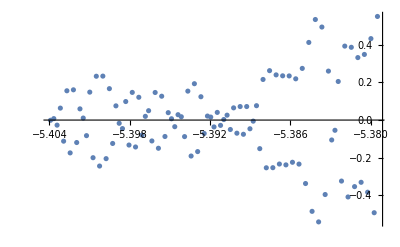

```mathematica
ListPlot[%]
```